# Impact of Urban Design on Quality of Life

## Intro

Most of the population around the globe is now concentrated in cities. There are around 2 dozens urban areas with populations exceeding 10 million people, but we still fail to quantify the influence of various aspects of urban design on the quality of life.
This work is a stepping stone in that direction.

## What is quality of life?

This is a very non-trivial question and we are not going to answer it in this work. Instead we will define a very simple approximation of quality of life as average sentiment across Tweets related to that specific city.

```mathematica
EstimateSentimentWL[sentence_String] := Module[{probs, pPos, pNeu, pNeg, resultPositivness, resultCertainity},
	probs = Classify["Sentiment", sentence, "Probabilities"];
	pPos = Lookup[probs, "Positive"];
	pNeu = Lookup[probs, "Neutral"];
	pNeg = Lookup[probs, "Negative"];
	resultPositivness = (pPos + pNeu * 0.5);
	resultCertainity = Max[probs];
	{resultPositivness,resultCertainity}
];
EstimateSentiments[sentences_, func_] := Map[({#, func[#]}) &, sentences];
EstimateSentiments[sentences_] := EstimateSentiments[sentences, EstimateSentimentWL];
RescaleIntoInterval[numbers_List, numberNewSmallest_, numberNewLargest_] := Map[(# * (numberNewLargest - numberNewSmallest) + numberNewSmallest) &, Rescale[numbers]];
```

## Which regions are we going to analyze?

rer

```mathematica
constantDirectory = "/Users/ashvardanian/CodeMine/WolframSummer19/Final Project/Drafts";
constantPathTweets = StringJoin[{constantDirectory, "/Tweets"}];
constantPathFeatures = StringJoin[{constantDirectory, "/Features"}];
constantPathMaps = StringJoin[{constantDirectory, "/Maps"}];
constantCityDiameterKM = 10;
constantCityGridSize = 5;
(* 
Ordered list of cities: https://www.timeout.com/things-to-do/best-cities-in-the-world 
Other lists can be found in "CitiesLists.nb".
*)
citiesPopular = {
Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Melbourne","Victoria","Australia"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"London","GreaterLondon","UnitedKingdom"}],Entity["City",{"LosAngeles","California","UnitedStates"}],Entity["City",{"Montreal","Quebec","Canada"}],Entity["City",{"Berlin","Berlin","Germany"}],Entity["City",{"Glasgow","GlasgowCity","UnitedKingdom"}],Entity["City",{"Paris","IleDeFrance","France"}],Entity["City",{"Tokyo","Tokyo","Japan"}],
Entity["City",{"Madrid","Madrid","Spain"}],Entity["City",{"CapeTown","WesternCape","SouthAfrica"}],Entity["City",{"LasVegas","Nevada","UnitedStates"}],Entity["City",{"MexicoCity","DistritoFederal","Mexico"}],Entity["City",{"Manchester","NewHampshire","UnitedStates"}],Entity["City",{"Philadelphia","Pennsylvania","UnitedStates"}],Entity["City",{"Barcelona","Barcelona","Spain"}],Entity["City",{"BuenosAires","BuenosAires","Argentina"}],Entity["City",{"Lisbon","Lisboa","Portugal"}],Entity["City",{"Washington","DistrictOfColumbia","UnitedStates"}],
Entity["City",{"TelAvivYafo","TelAviv","Israel"}],Entity["City",{"Bombay","Maharashtra","India"}],Entity["City",{"Toronto","Ontario","Canada"}],Entity["City",{"Birmingham","Alabama","UnitedStates"}],Entity["City",{"Dublin","Dublin","Ireland"}],Entity["City",{"SaoPaulo","SaoPaulo","Brazil"}],Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"Porto","Norte","Portugal"}],Entity["City",{"Singapore","Singapore","Singapore"}],Entity["City",{"Edinburgh","Edinburgh","UnitedKingdom"}],
Entity["City",{"SanFrancisco","California","UnitedStates"}],Entity["City",{"Dubai","Dubai","UnitedArabEmirates"}],Entity["City",{"Munich","Bavaria","Germany"}],Entity["City",{"Vienna","Vienna","Austria"}],Entity["City",{"Shanghai","Shanghai","China"}],Entity["City",{"Moscow","Moscow","Russia"}],Entity["City",{"Delhi","Delhi","India"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"Sydney","NewSouthWales","Australia"}],Entity["City",{"AbuDhabi","AbuDhabi","UnitedArabEmirates"}],
Entity["City",{"HongKong","HongKong","HongKong"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"RioDeJaneiro","RioDeJaneiro","Brazil"}],Entity["City",{"Marseille","ProvenceAlpesCoteDAzur","France"}],Entity["City",{"Bangkok","Bangkok","Thailand"}],Entity["City",{"KualaLumpur","KualaLumpur","Malaysia"}],Entity["City",{"Beijing","Beijing","China"}],Entity["City",{"Istanbul","Istanbul","Turkey"}]
};
CityName[city_] := EntityValue[city, "Name"];
CityDataPath[directory_String, city_String] := StringJoin[{directory, "/", city, ".mx"}];
CityDataPath[directory_String, city_] := CityDataPath[directory, CityName[city]];
```

Lets collect Twitter data.

```mathematica
tw = ServiceConnect["Twitter"];
TwDownloadCity[city_] := Module[{name, data, path},
	name = CityName[city];
	path = CityDataPath[constantPathTweets, name];
	data = tw["TweetSearch", "Query"->name];
	Export[path, data, OverwriteTarget->True];
	data
];
TwPullCity[city_] := Module[{data, path},
	path = CityDataPath[constantPathTweets, city];
	data = If[FileExistsQ[path], Import[path], TwDownloadCity[city]];
	Normal[data]
];
TwEstimateQualityOfLife[city_] := Module[{data, tweetsWSentiments, sentimentsWCertainity, meanPositivness, meanCertainty},
	data = TwPullCity[city];
	data = data⟦All, "Text"⟧;
	tweetsWSentiments = EstimateSentiments[data];
	sentimentsWCertainity = tweetsWSentiments⟦All, 2⟧;
	meanPositivness = MeanAround[sentimentsWCertainity⟦All, 1⟧];
	meanCertainty = MeanAround[sentimentsWCertainity⟦All, 2⟧];
	{meanPositivness, meanCertainty}
];
```

Once we collect the data from Twitter, we want to see how the

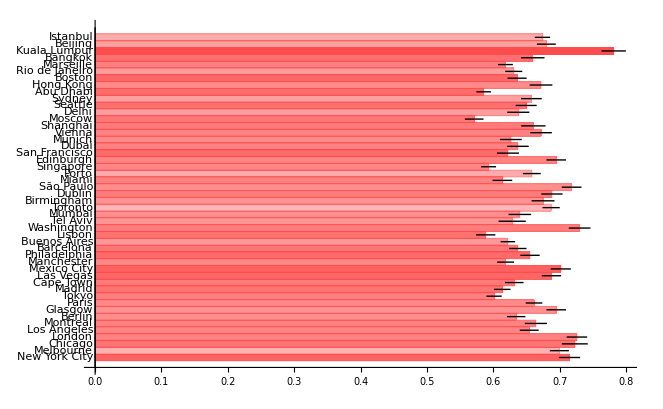

```mathematica
citiesEstimates = Map[TwEstimateQualityOfLife, citiesPopular];
citiesCertainties = RescaleIntoInterval[Map[(#["Value"]) &, citiesEstimates⟦All, 2⟧], 0.4, 1];
citiesColors = Map[RGBColor[1, 0.3, 0.3, #] &, citiesCertainties];
citiesPositivness = citiesEstimates⟦All, 1⟧;
BarChart[citiesPositivness,ChartLabels->Map[CityName, citiesPopular],BarOrigin->Left,ChartStyle->citiesColors]
```

As we can see, there is not much variance between cities, in terms of Tweets sentiment.
Lets compile multiple rankings together, assuming that they have had a more complete model for estimating the quality of life and satisfaction.

```mathematica
citiesPositivness = RescaleIntoInterval[Map[(N[1/#])&, Range[Length[citiesPopular]]], 0.6, 1];
```

## Are there any correlations at all?

wew

```mathematica
ExtractMaps[city_] := Module[{cityBounds, gridLats, gridLons, cityParts, cityImages, MakeCell, ImageForCell},
	cityBounds = Normal[GeoBoundingBox[GeoPosition[city], Quantity[constantCityDiameterKM,"Kilometers"]]];
	gridLats = Subdivide[Latitude[cityBounds⟦1⟧],Latitude[cityBounds⟦2⟧], constantCityGridSize+1];
	gridLons = Subdivide[Longitude[cityBounds⟦1⟧],Longitude[cityBounds⟦2⟧], constantCityGridSize+1];
	MakeCell[i_Integer, j_Integer] := GeoRange[{gridLats⟦i⟧, gridLats⟦i+1⟧}, {gridLons⟦j⟧, gridLons⟦j+1⟧}];
	cityParts = Flatten[Table[MakeCell[i, j], {i, constantCityGridSize}, {j, constantCityGridSize}]];
	ImageForCell[coords_] := Module[{coordsAsList},
		coordsAsList = List @@ coords;
		Image[GeoGraphics[GeoRange->coordsAsList]]
	];
	cityImages = Map[ImageForCell, cityParts]
];
ExportMaps[city_] := Export[CityDataPath[constantPathMaps, city],ExtractMaps[city]];
ImportMaps[city_] := Import[CityDataPath[constantPathMaps, city]];
```

```mathematica
ExtractListFeatures[object_, props_List] := Normal[Map[({#, Normal[object[#]]}) &, props]];
ExtractCityStatsFeatures[city_] := Module[{props}, 
	props = {"Population","Latitude","Longitude","Elevation","MagneticFieldStrength"};
	ExtractListFeatures[city, props]
];
ExtractCountryStatsFeatures[city_] := Module[{props, country},
	country = city["Country"];
	props = {"Population","Latitude","Longitude",
	"Area","WaterArea","BoundaryLength",
	"ChildPopulation","ContributingFamilyWorkers","ElderlyPopulation","HIVAIDSPopulation",
	"NetIncomeFromAbroad","GovernmentDebt","GovernmentSurplus","ImportsValue","ExportsValue",
	"GiniIndex","Army"};
	ExtractListFeatures[country, props]
];
ExtractMapFeatures[city_] := Module[{},
	List[]
];
ExtractAllFeatures[city_] := Join[ExtractCityStatsFeatures[city], ExtractCountryStatsFeatures[city], ExtractMapFeatures[city]];
ExportAllFeatures[city_] := Export[CityDataPath[constantPathFeatures, city], ExtractAllFeatures[city]];
ImportAllFeatures[city_] := Import[CityDataPath[constantPathFeatures, city]];
```

```mathematica
Map[ExportMaps, citiesPopular]
```

GeoGraphics::wdata: Unable to download data for ranges {{-86.9067,-86.8708},{35.5148,35.5509}} and zoom level 15 from the Wolfram geo server.

GeoGraphics::tiles: Unable to download 3 tiles of the geo background image.

```mathematica
citiesFeatures =Map[ImportAllFeatures[#]⟦All, 2⟧ &, citiesPopular];
```

```mathematica
p=Predict[citiesFeatures->citiesPositivness,Method->"LinearRegression"]
```

PredictorFunction[…]

## Are there correlations between cities topology and quality of life?

wewe

## Are there correlations between known features and quality of life?

wewe